```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/";
```

```mathematica
CI[boots_]:=Block[{LQ,UQ,upper,lower},
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
upper=Quantile[boots,UQ];
lower=Quantile[boots,LQ];
(upper-lower)/2];
```

```mathematica
makePlots=
```

## α=0.2

```mathematica
α=0.2;
V=4/3α;
steps=500;
```

### NLO

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/";
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers10000_Ncoord2_Nc3_Nf5_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{501,10000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

501

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

10000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{501,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.038720.00009

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.040560.00004

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers10000_Ncoord2_Nc3_Nf5_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep100_Nwalkers10000_Ncoord2_Nc3_Nf5_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.040250.00008

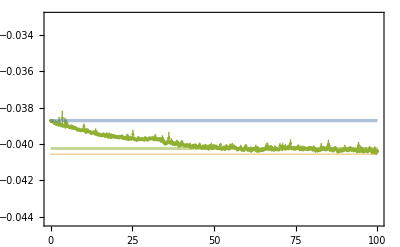

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

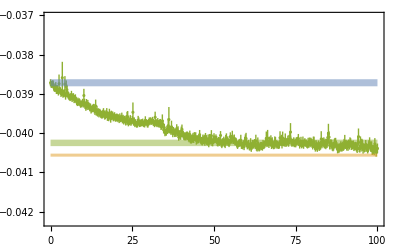

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.05Egfmc[[1]],.92Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.00780.0023

```mathematica
(Egfmc-ET)/Egfmc
```

0.03800.0030

```mathematica
2/V
```

7.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

1.67877

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

## α=0.6

```mathematica
α=0.6;
V=4/3α;
steps=100;
```

### NLO

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/";
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers10000_Ncoord2_Nc3_Nf5_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{101,10000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

10000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.72460.0024

```mathematica
Evmc=V^2Around[-1.283178687095642,0.00400820467621088]
```

-0.82120.0026

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers10000_Ncoord2_Nc3_Nf5_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep100_Nwalkers10000_Ncoord2_Nc3_Nf5_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.83710.0026

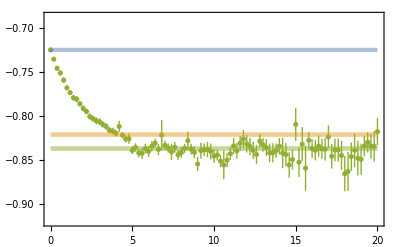

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0190.004

```mathematica
(Egfmc-ET)/Egfmc
```

0.1340.004

```mathematica
2/V
```

2.5

```mathematica
a=1.7029
```

1.7029

```mathematica
a V
```

1.36232

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```